```mathematica
f[x_]:=x^2-3
```

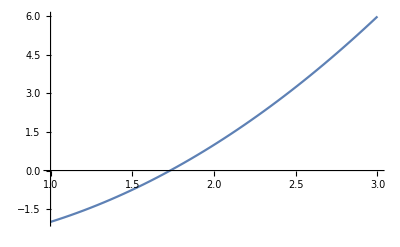

```mathematica
Plot[f[x],{x,1,3}]
```

```mathematica
x=5.;
delx=1.;
n=0;

While[delx>0.0001,x0=x;
x=x-f[x]/f'[x];
delx=Abs[x0-x];
n++]

Print["xRoot ","after ",n," times: ",x]
```

xRoot after 5 times: 1.73205